```mathematica
(*GaAs parameters-can be changed*)γ1=6.98;
γ2=2.06;
γ3=2.93;
b=-2;   (*eV*)
d=-4.8;  (*eV*)

(*Compliance constants for GaAs in Pa^-1*)
S11=1.1638834280282574*^-13;
S12=-3.605068158741818*^-14;
S44=1.6778523489932887*^-13;

(*Strain parameters as functions of stress σ (in Pa)*)
α[σ_]:=(1/2)(S11+S12) σ
β[σ_]:=(1/2) S44 σ

(*Denominator*)
Δ[σ_]:=Sqrt[b^2 α[σ]^2+d^2 β[σ]^2]

(*Effective mass functions-m0=1*)
(*mhx:along[110]-stress direction*)
mhx[γ1_,γ2_,γ3_,b_,d_,σ_]:=1/(γ1+(Sqrt[3] γ3 d β[σ]+γ2 b α[σ])/Δ[σ])

(*mhy:along[1-10]-in-plane transverse*)
mhy[γ1_,γ2_,γ3_,b_,d_,σ_]:=1/(γ1-(Sqrt[3] γ3 d β[σ]-γ2 b α[σ])/Δ[σ])

(*mhz:along[001]-out-of-plane*)
mhz[γ1_,γ2_,γ3_,b_,d_,σ_]:=1/(γ1-(2 γ2 b α[σ])/Δ[σ])

(*Example:evaluate at 1 GPa compressive stress (σ=-1e9 Pa)*)
σtest=-1*10^9;
(* tratio is \tau_h/\tau_e *)
mhxu[σ_]:=mhx[γ1,γ2,γ3,b,d,σ]
mhyu[σ_]:=mhy[γ1,γ2,γ3,b,d,σ]
mhzu[σ_]:=mhz[γ1,γ2,γ3,b,d,σ]
mh3u[σ_]:=mhxu[σ]*mhyu[σ]*mhzu[σ]
xterm[σ_,me_,tratio_]:=(mhxu[σ]/me) - tratio*Sqrt[mh3u[σ]/(me^3)]
yterm[σ_,me_,tratio_]:=(mhyu[σ]/me) - tratio*Sqrt[mh3u[σ]/(me^3)]
zterm[σ_,me_,tratio_]:=(mhzu[σ]/me) - tratio*Sqrt[mh3u[σ]/(me^3)]
checkADCPxy[σ_,me_,tratio_]:=xterm[σ,me,tratio]*yterm[σ,me, tratio]
checkADCPzy[σ_,me_,tratio_]:=zterm[σ,me,tratio]*yterm[σ,me,tratio]
checkADCPxz[σ_,me_,tratio_]:=zterm[σ,me,tratio]*xterm[σ,me,tratio]

(*Geometric mean*)
mlh[γ1_,γ2_,γ3_,b_,d_,σ_]:=(mhx[γ1,γ2,γ3,b,d,σ]*mhy[γ1,γ2,γ3,b,d,σ]*mhz[γ1,γ2,γ3,b,d,σ])^(1/3)

Print["mlh geom. mean = ",mlh[γ1,γ2,γ3,b,d,σtest]," m0"]
```

mlh geom. mean = 0.17594 m0

```mathematica
xterm[10000, 0.063,2]
```

-0.6221

```mathematica
{mhx[γ1,γ2,γ3,b,d,0.1],mhx[γ1,γ2,γ3,b,d,10], mhx[γ1,γ2,γ3,b,d,100], mhx[γ1,γ2,γ3,b,d,10^5],mhx[γ1,γ2,γ3,b,d,10^9], mhx[γ1,γ2,γ3,b,d,10^12]}
```

{0.624949,0.624949,0.624949,0.624949,0.624949,0.624949}

```mathematica
{mhxu[0.1],mhxu[10],mhxu[100],mhxu[10^5],mhxu[10^9],mhxu[10^12]}
```

{0.624949,0.624949,0.624949,0.624949,0.624949,0.624949}

```mathematica
{mhxu[10^9],mhyu[10^9],mhzu[10^9]}
```

{0.624949,0.0865517,0.128434}

```mathematica
(* checking ADCP between different directions*)
```

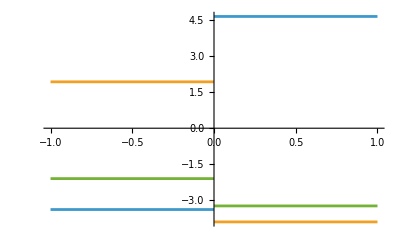

```mathematica
Plot[{xterm[t,0.063],yterm[t,0.063],zterm[t,0.063]},{t,-1,1},PlotRange->All]
```

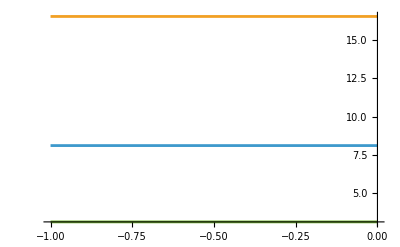

```mathematica
Plot[{checkADCPxy[t,0.063,0.01],checkADCPzy[t,0.063,0.01], checkADCPxz[t,0.063,0.01]},{t,-10^9,0},PlotRange->All]
```

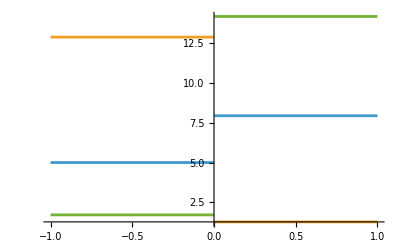

```mathematica
Plot[{checkADCPxy[t,0.063,0.1],checkADCPzy[t,0.063,0.1], checkADCPxz[t,0.063,0.1]},{t,- 1,1},PlotRange->All]
```

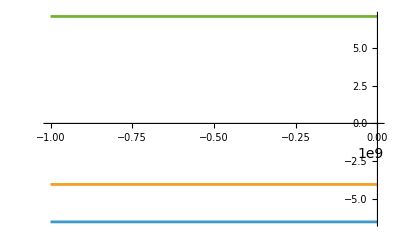

```mathematica
Plot[{checkADCPxy[t,0.063,1],checkADCPzy[t,0.063,1], checkADCPxz[t,0.063, 1]},{t,- 10^9,0},PlotRange->All]
```

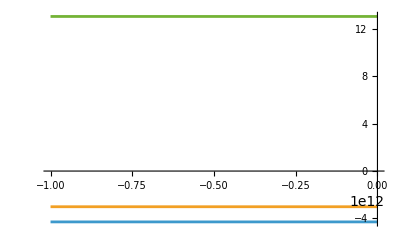

```mathematica
Plot[{checkADCPxy[t,0.063,1.2],checkADCPzy[t,0.063,1.2], checkADCPxz[t,0.063, 1.2]},{t,- 10^12,0},PlotRange->All]
```

```mathematica
(* checking ADCP with fixed stress and varying relaxation parameter ratio \tau = \tau_h/\tau_e*)
```

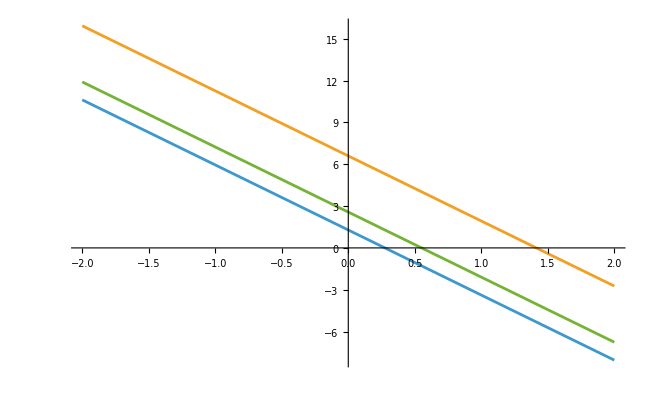

```mathematica
Plot[{xterm[-10^9,0.063,t],yterm[-10^9,0.063,t],zterm[-10^9,0.063, t]},{t,-2,2},PlotRange->All]
```

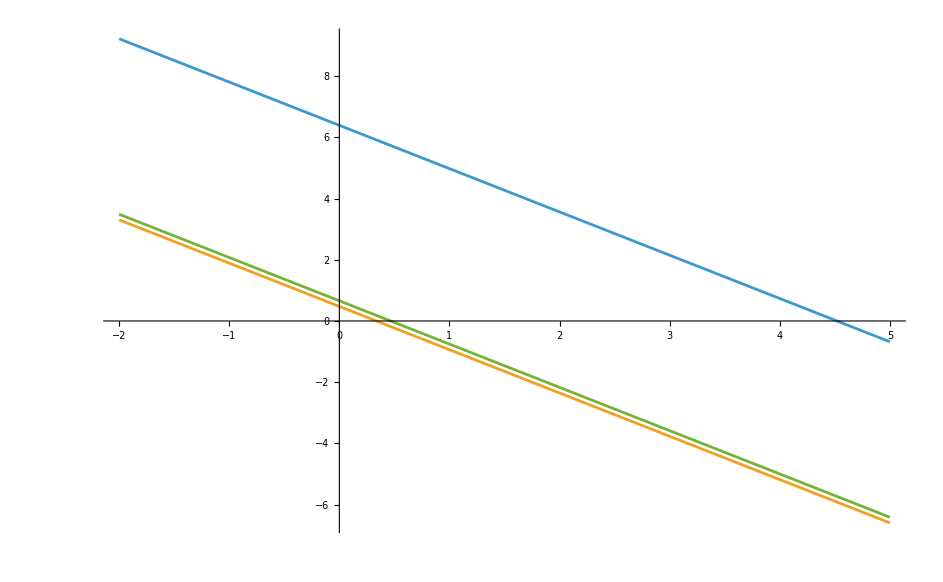

```mathematica
Plot[{xterm[10^9,0.063,t],yterm[10^9,0.063,t],zterm[10^9,0.063, t]},{t,-2,5},PlotRange->All]
```

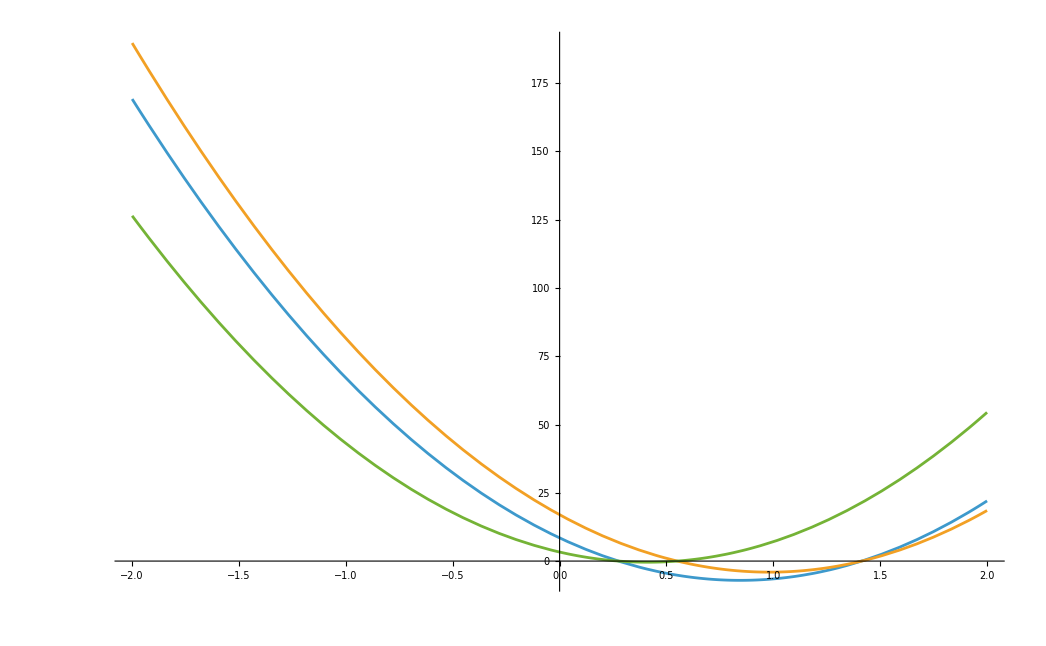

```mathematica
Plot[{checkADCPxy[-10^9,0.063,t],checkADCPzy[-10^9,0.063,t], checkADCPxz[-10^9,0.063, t]},{t,-2,2},PlotRange->All]
```

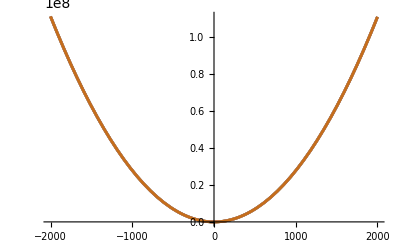

```mathematica
Plot[{checkADCPxy[0.1,0.063,t],checkADCPxy[1,0.063,t],checkADCPxy[100,0.063,t],checkADCPxy[10^6,0.063,t],checkADCPxy[10^9,0.063,t],checkADCPxy[10^12,0.063,t]},{t,-2000,2000},PlotRange->All]
```

```mathematica
mex = 0.063
mey = 0.063
mez = 0.063
me3 = 0.063^3
mhxu = 0.08907
mhyu = 0.415592
mhzu = 0.161972
mh3u = mhxu*mhyu*mhzu
```